```mathematica
f[t_]:=UnitStep[t+1]
```

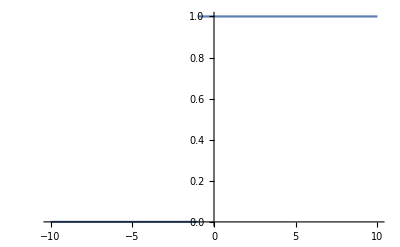

```mathematica
Plot[f[t],{t,-10,10}] (* time domain plot *)
```

```mathematica
F=LT[f[t],t,s]
```

ConditionalExpression[ⅇ^s/s,Re[s]>0]

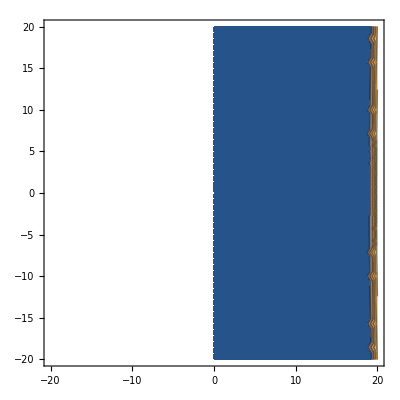
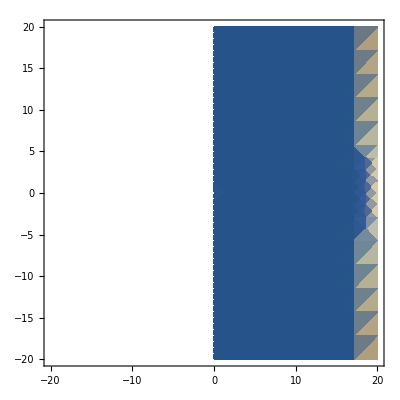
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
Block[{s=σ+I ω},Table[plot[Abs[F],{σ,-20,20},{ω,-20,20},PlotRange->Full],{plot,{Plot3D,ContourPlot,DensityPlot}}]]
```